# Experiment 25 - Balmer Lines of Hydrogen and Deuterium

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Peak-finding function

To make the calibration process easier, we write a quick algorithm to find peaks in a reasonably-restricted dataset (in the broad spectra, finding peaks quickly becomes intractable because of noise and complex features in the spectra not corresponding to Balmer lines), and a second function to find the full-width at half maximum in restricted datasets with a single peak.

```mathematica
(* Finds peaks and displays plots for visual confirmation. Selects for peaks that survive Gaussian blurring σ to account for noise *)
peakEstimate[filename_,σ_]:=
Module[{data,rawData,peaks,listPeaks,interFun,p1,p2},(data=Import[filename];
rawData=Table[If[data[[i]][[1]]=="#",Null,data[[i]]],{i,1,Length[data]}]/.Null->Sequence[]; (* removing comments and headers from data *)
peaks=FindPeaks[rawData[[All,2]],σ]; (* we select for peaks surviving a Gaussian blurring with σ to account for noise *)
listPeaks=Table[rawData[[Floor[peaks[[i]][[1]]]]],{i,1,Length[peaks]}];
interFun=Interpolation[rawData];
p1=ListLogPlot[listPeaks,PlotRange->{{rawData[[1]][[1]],rawData[[Length[rawData]]][[1]]},{0.9 Min[rawData[[All,2]]],All}},FrameLabel->{"Wavelength (nm)","Intensity"}];
p2=LogPlot[interFun[x],{x,rawData[[1]][[1]],rawData[[Length[rawData]]][[1]]},FrameLabel->{"Wavelength (nm)","Intensity"}];
{listPeaks,Show[p1,p2,ImageSize->315]})]
```

```mathematica
(* Finds full-width at half-maximum for a selected peak, assuming the section in the file has a single peak as only feature. This should be sufficient for the calibration data. *)
fwhm[filename_,peakLocation_]:=Module[{data,rawData,interFun,halfMax,lowHalf,highHalf,x,y},(data=Import[filename];
rawData=Table[If[data[[i]][[1]]=="#",Null,data[[i]]],{i,1,Length[data]}]/.Null->Sequence[]; (* removing comments and headers from data *)
interFun=Interpolation[rawData];
halfMax=Min[rawData[[All,2]]]+(peakLocation[[2]]-Min[rawData[[All,2]]])/2;
lowHalf=x/.FindRoot[interFun[x]==halfMax,{x,peakLocation[[1]]+0.1,peakLocation[[1]],rawData[[Length[rawData]]][[1]]}];
highHalf=y/.FindRoot[interFun[y]==halfMax,{y,peakLocation[[1]]-0.1,rawData[[1]][[1]],peakLocation[[1]]}];
Abs[highHalf-lowHalf])]
```

## Calibrating the Monochromator using NIST data for the Hg-lines

We calibrate the monochromator (note that we will be doing all observations in second order, therefore we calibrate our second order observations with the actual lines in first order) and expect a linear fit with slope ~2. We have to go up to a Gaussian smoothing with σ=28 to get rid of unwanted peaks, at which point the functions accurately finds all desired line positions. (See table below, where we show a plot of the peaks and the estimated line positions for visual confirmation that the function is performing as desired.)

We estimate the uncertainties in peak position by FWHM/2.355, where FWHM is the full-width at half-maximum. We cannot determine an accurate, independent line position uncertainty for each line, so we use the width of the peaks as a rough measure of the uncertainty in the line positions. If our lines were somehow convolved with a Gaussian scattering function as a result of our sources of uncertainty, we would expect the standard deviation to be a measure of the uncertainty in our line position, hence our choice of 2.355*FWHM. (Of course, we have no idea as to whether the sources of uncertainty act by any stretch in a Gaussian manner on our measurements, but this is the simplest assumption to make and we have no information to help us make a better guess.) This should at least provide an upper bound on the error in peak location.

```mathematica
calList={"365119.dat","365588.dat","366432.dat","404770.dat","435955.dat","546226.dat","577120.dat","579227.dat"};
```

```mathematica
(* We pull the expected wavelength from NIST data from the comment added to each file *)
nist[filename_]:=Module[{data},(data=Import[filename];data[[1]][[2]])]
```

```mathematica
hgPeaks={#,nist[#],Flatten[peakEstimate[#,28][[1]],1][[1]],Flatten[peakEstimate[#,28][[1]],1][[2]],peakEstimate[#,28][[2]]}&/@calList;
```

```mathematica
unc=1/2.355 fwhm[#[[1]],{#[[3]],#[[4]]}]&/@hgPeaks;
```

```mathematica
calTable=Join[{{"NIST
 Position (nm)","Observed 
Position (nm)","Estimated 
Uncertainty (nm)","Plot of Peak"}},Table[{hgPeaks[[i]][[2]],hgPeaks[[i]][[3]],unc[[i]],hgPeaks[[i]][[5]]},{i,1,Length[hgPeaks]}]];
```

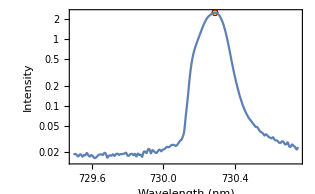
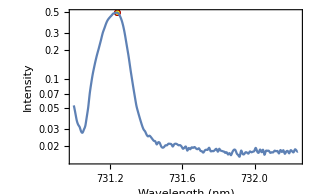
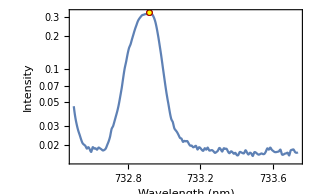
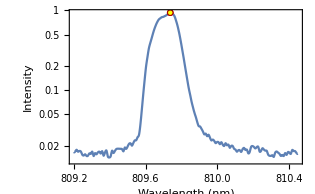
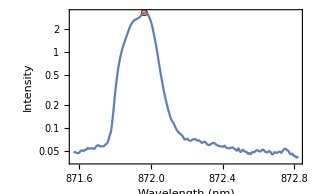
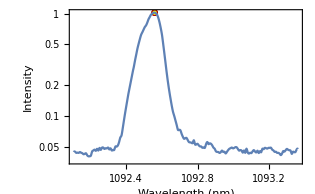
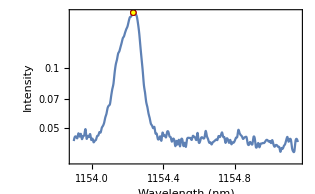
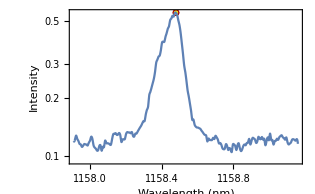
NIST
 Position (nm) | Observed 
Position (nm) | Estimated 
Uncertainty (nm) | Plot of Peak
365.119 | 730.287 | 0.0593201 | -Graphics-
365.588 | 731.242 | 0.0586332 | -Graphics-
366.432 | 732.919 | 0.0667756 | -Graphics-
404.77 | 809.738 | 0.0653051 | -Graphics-
435.955 | 871.964 | 0.0644367 | -Graphics-
546.226 | 1092.56 | 0.0562492 | -Graphics-
577.12 | 1154.23 | 0.0565783 | -Graphics-
579.127 | 1158.48 | 0.0576036 | -Graphics-

```mathematica
Grid[calTable,Alignment->Left,Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{Gray,None}}]
```

```mathematica
(* Having confirmation that our peak-finding function performs satisfactorily in finding estimates of line positions from our data, we use our observed line positions along with the NIST data to calibrate the monochromator for observations in 2^nd order. We simply export the dataset above and perform a linear fit without uncertainties using CurveFit. *)
```

```mathematica
calSet=Join[{{"S NIST_Position(nm)","Observed_Position(nm)"}},Drop[calTable[[All,{1,2}]],1]];
```

```mathematica
Export["hgCalibration.dat",calSet];
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 25/hgCalibration.dat

File comment header:

NIST_Position(nm)	Observed_Position(nm)

Read 8 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 8

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00886674 | b= 
0.499958 | 
σ_a= 
0.0767795 | σ_b= 
0.0000827381 | Std. deviation= 
0.0423372

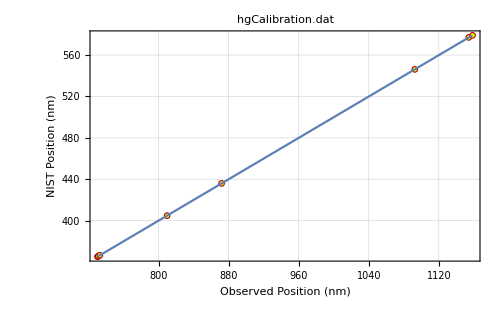
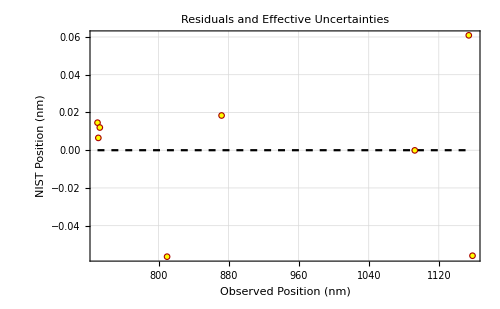
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.00886674 | b= 
0.499958 | 
σ_a= 
0.0767795 | σ_b= 
0.0000827381 | Std. deviation= 
0.0423372

```mathematica
LinearDifferencePlot[FrameLabel->{"Observed Position (nm)","NIST Position (nm)"}]
```

We observe that the maximum deviation from our linear fit is 0.06 nm, and our maximum fractional deviation from the fit is ~0.007% (at the 809.738 nm data point). This is a rather small fractional error, and along with the spread of the deviations from the fit, indicates that a linear fit is adequate to calibrate the monochromator for observations in second order.

The slope of 0.499958 ± 0.000083 is consistent with the expected value of 0.5 for second order diffraction, so it is difficult to tell whether the index of refraction of air in the lab or some other source of error affected our calibration in any way. However, for our purposes a slope within error of 0.5 indicates that any such source of error has a negligible effect on our calibration.

## Locating the Balmer lines

### Processing data points

```mathematica
(* First, we have to process our data for the line observed at 794nm, as it was not obtained using a single scan. We simply average over multiple scans to obtain a reasonable signal. *)
Module[{data,rawData,avg},(data=Import["Balmer/h794.dat"];rawData=Table[If[data[[i]][[1]]=="#",Null,data[[i]]],{i,1,Length[data]}]/.Null->Sequence[]; (* removing comments and headers from data *);avg=Mean/@GatherBy[rawData,First];Export["Balmer/avg794.dat",avg])];
```

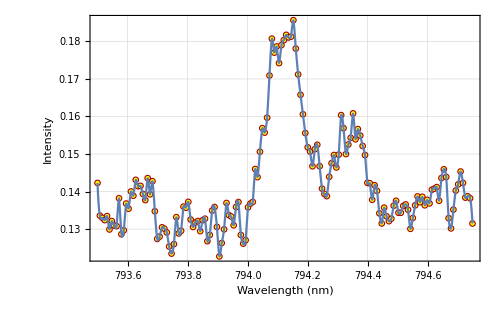

```mathematica
data2=Import["Balmer/avg794.dat"];
before1=ListPlot[data2,FrameLabel->{"Wavelength (nm)","Intensity"}];
beforeFun=Interpolation[data2];
before2=Plot[beforeFun[x],{x,data2[[1]][[1]],data2[[Length[data2]]][[1]]},FrameLabel->{"Wavelength (nm)","Intensity"}];
Show[before1,before2]
```

```mathematica
(* The resulting data is nevertheless very noisy, making it very difficult to reliably identify a peak in the interpolated function. We therefore perform a moving average with a window of 5 data points to make it possible to identify peaks in our data, and restrict our data to our Balmer lines of interest. *)
```

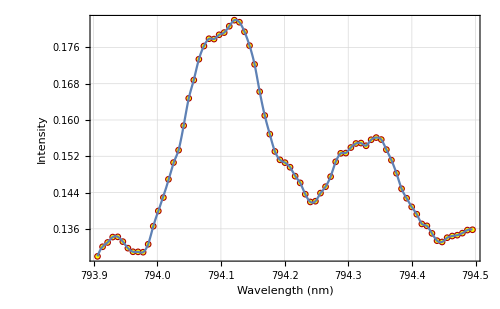

```mathematica
data3=MovingAverage[data2[[All,2]],5];
data4=Partition[Riffle[data2[[All,1]],data3],2];
data5=Select[data4,793.9<#[[1]]<794.5&];
afterFun=Interpolation[data5];
after1=ListPlot[data5,FrameLabel->{"Wavelength (nm)","Intensity"}];
after2=Plot[afterFun[x],{x,data5[[1]][[1]],data5[[Length[data5]]][[1]]},FrameLabel->{"Wavelength (nm)","Intensity"}];
Show[after1,after2]
```

```mathematica
Export["Balmer/movingAvg794.dat",data5];
```

```mathematica
(* Because of the noise in the data (recall that the hydrogen lamp gets dim very fast), we have to restrict our dataset to our Balmer peaks of interest in order for our function to be able to pick our peaks. We also perform a moving average as before to get a better peak location, as some of the peaks can be displaced by noise near the peaks. *)
```

```mathematica
SetDirectory["Balmer"];
```

```mathematica
trim[filename_,range_]:=Module[{data,rawData,avgData,avgList,trimmed},(data=Import[filename];rawData=Table[If[data[[i]][[1]]=="#",Null,data[[i]]],{i,1,Length[data]}]/.Null->Sequence[]; avgData=MovingAverage[rawData[[All,2]],5];avgList=Partition[Riffle[rawData[[All,1]],avgData],2];trimmed=Select[avgList,range[[1]]<#[[1]]<range[[2]]&];Export[StringReplace["trim%","%"->filename],trimmed])]
```

```mathematica
trim["h820.dat",{820.2,820.65}];trim["h868.dat",{868.0,868.5}];trim["h972.dat",{972.05,972.65}];trim["h1312.dat",{1312.2,1313.1}];
```

### Balmer peaks and Deuterium shift

We can now use our data to locate the Balmer lines, and convert the observed values to line positions with uncertainties using our calibration.

```mathematica
balmer={"movingAvg794.dat","trimh820.dat","trimh868.dat","trimh972.dat","trimh1312.dat"};
```

```mathematica
obs=peakEstimate[#,5]&/@balmer;
```

```mathematica
(* We define our calibration function, such that it returns line positions along with propagated uncertainties. Since it is difficult to obtain anything more than an estimated upper bound on the uncertainties in observed line positions - because we only have one sweep for each peak - we use the FWHM on the Hydrogen peaks, as we had for the Hg-line calibration data. Using our FWHM function, we observe that the FWHM for all of our Balmer lines are very similar at ~0.1 nm, corresponding to a standard deviation of ~0.042 nm, very close to the standard deviation we have obtained for the calibration. *)
calFun[observation_]:={a+b observation,Sqrt[siga^2+observation b((0.1/(2.355 observation))^2+(sigb/b)^2)]}
(* However, our fit parameter a simply represents a systematic offset. Therefore, it does not affect the shift in the Balmer lines, since λ^D and λ^H are measured in a single scan for each data point. We can then obtain the corrected shift using the slope of the calibration function only, such that the uncertainty in the shift is only determined by the uncertainty in the fit parameter b. We can see, as shown below, that this entails that we know the separation with greater accuracy than we know the individual line positions. *)
calShift[obsλD_,obsλH_]:=(obsλH-obsλD){b,b Sqrt[(0.1/(2.355 (obsλH-obsλD)))^2+(sigb/b)^2]}
```

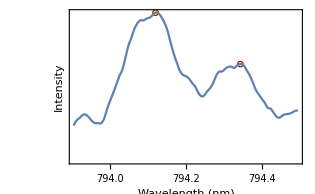
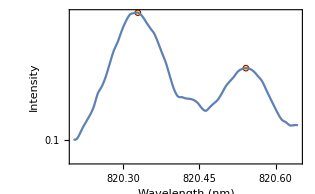
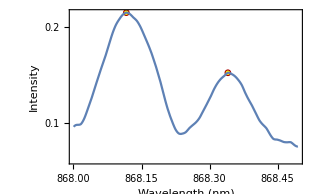
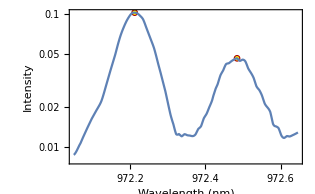
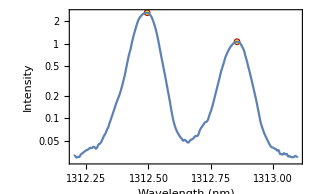
λ^D (nm) | λ^H (nm) | λ^H-λ^D (nm) | Plot of Balmer peaks
397.019 ± 0.0769 | 397.13 ± 0.0769 | 0.111453 ± 0.0212 | -Graphics-
410.122 ± 0.0769 | 410.228 ± 0.0769 | 0.106127 ± 0.0212 | -Graphics-
434.013 ± 0.0769 | 434.125 ± 0.0769 | 0.11188 ± 0.0212 | -Graphics-
486.057 ± 0.0769 | 486.193 ± 0.0769 | 0.136022 ± 0.0212 | -Graphics-
656.184 ± 0.0769 | 656.364 ± 0.0769 | 0.180201 ± 0.0212 | -Graphics-

```mathematica
balmerLines=Module[{dObs,hObs},Table[{calFun[dObs=obs[[i]][[1]][[1]][[1]]],calFun[hObs=obs[[i]][[1]][[2]][[1]]],calShift[dObs,hObs],obs[[i]][[2]]},{i,1,Length[obs]}]];
balmerGrid=Join[{{"λ^D (nm)","λ^H (nm)","λ^H-λ^D (nm)","Plot of Balmer peaks"}},Table[{StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[balmerLines[[i]][[1]][[1]],6]],"%2"->ToString[NumberForm[balmerLines[[i]][[1]][[2]],3]]}],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[balmerLines[[i]][[2]][[1]],6]],"%2"->ToString[NumberForm[balmerLines[[i]][[2]][[2]],3]]}],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[balmerLines[[i]][[3]][[1]],6]],"%2"->ToString[NumberForm[balmerLines[[i]][[3]][[2]],3]]}],balmerLines[[i]][[4]]},{i,1,Length[balmerLines]}]];
Grid[balmerGrid,Alignment->Left,Frame->All,ItemStyle->"Text",Background->{{None,None},{Gray,None}}]
```

## Line separations and Hydrogen line wavelengths

```mathematica
(* We export the hydrogen line wavelength and line separation data for analysis in CurveFit. *)
hdData=Join[{{"S lambdaH(nm)","shift(nm)","sigmaShiftH(nm)","sigmaLambdaH"}},Table[{balmerLines[[i]][[2]][[1]],balmerLines[[i]][[3]][[1]],balmerLines[[i]][[3]][[2]],balmerLines[[i]][[2]][[2]]},{i,1,Length[balmerLines]}]];
Export["sepData.dat",hdData];
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

```mathematica
LinearFit[]
```

n = 5

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.00787385 | b= 
0.000287349 | 
σ_a= 
0.0122031 | σ_b= 
0.0000251021 | Std. deviation= 
0.00532107

Fit of (x,y±σ_y)

a= 
-0.00787385 | b= 
0.000287349 | 
σ_a= 
0.114661 | σ_b= 
0.000235861 | χ^2/(n-2)= 
0.0113274

Fit of (x±σ_x,y±σ_y)

a= 
-0.00787385 | b= 
0.000287349 | 
σ_a= 
0.114661 | σ_b= 
0.000235861 | χ^2/(n-2)= 
0.0113274

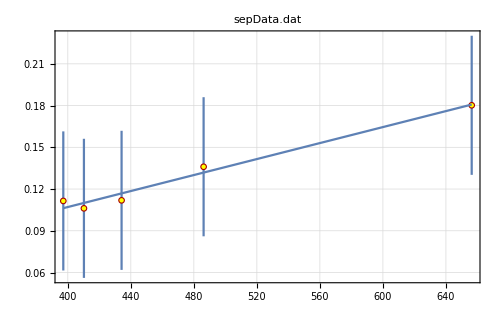
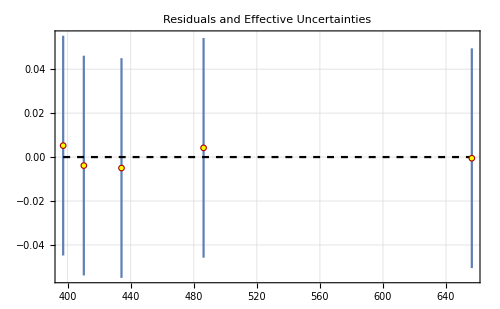
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.00787385 | b= 
0.000287349 | 
σ_a= 
0.114661 | σ_b= 
0.000235861 | χ^2/(n-2)= 
0.0113274

```mathematica
LinearDifferencePlot[]
```

We observe a large error in our fit parameters for our weighted fit, and a (χ̃)^2 well below 1, indicating that, as expected, the FWHM estimate of uncertainty in peak location was a large underestimate of the accuracy of the monochromator. We therefore use the parameters of the unweighted fit in the following analysis. From equation (11), we have (where b is the fit parameter for our fit of λ^H-λ^D against λ^H):

m_e/m_p=2b

```mathematica
ratio=2 {b,0.0000251}
```

{0.000574698,0.0000502}

Therefore we estimate m_e/m_p=(5.75±0.50)×10^-4. This is within error of the NIST value of 5.466×10^-4.

### Estimating Avogadro’s number

From the above, we estimate the proton rest energy as:

```mathematica
ep=0.511/ratio[[1]](* in MeV *)
```

889.163

We then estimate the mass of the hydrogen atom as:

```mathematica
mh=((ep+0.511)*10^6*1.602*10^-19)/((3*10^8)^2)(*in kg *)
```

1.58362×10^-27

If a mole of H_2 masses 2g, we can then estimate Avogadro’s number as:

```mathematica
na=0.002/(2(mh))(* in mol^-1 *)
```

6.31465×10^23

which is reasonably close to the NIST value of 6.033*10^23 mol^-1.

## Optional observation: line at 508 nm

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 25/weird 508UV smaller order].dat

File comment header:

Weird 508 smaller order
Spectrum #00116	6:18:22 PM 4/26/2018
Narrow scan: start 506.87nm, end 508.12nm
Monochromator settings: Grating: 1200 lines/mm; Slits: entrance 20um, exit 20um.
DAQ device: PCI-6221; ADC bits: 16; Settling time: 10ms
ADC input range: 10V max, -10V min. Sampling: 400 samples at 6.0006k/second.
Wavelength (nm)    Signal (V)

Read 146 data points.

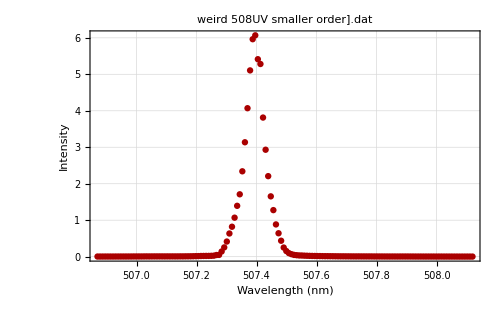

```mathematica
LinearDataPlot[FrameLabel->{"Wavelength (nm)","Intensity"}]
```

We observe this feature at 507.4 nm, which seems to disappear if we use the clear filter. Since the clear filter should let 507.4 nm light through (cyan), we deduce that we are observing a lower wavelength feature in higher order. In fact this corresponds to an observation in second order of a strong line in the NIST database at 253.48 nm.

We can observe the feature in fourth order:

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 25/weird 508UV.dat

File comment header:

Weird 508
Spectrum #00112	5:58:39 PM 4/26/2018
Narrow scan: start 1014.4nm, end 1015.64nm
Monochromator settings: Grating: 1200 lines/mm; Slits: entrance 20um, exit 20um.
DAQ device: PCI-6221; ADC bits: 16; Settling time: 10ms
ADC input range: 10V max, -10V min. Sampling: 400 samples at 6.0006k/second.
Wavelength (nm)    Signal (V)

Read 175 data points.

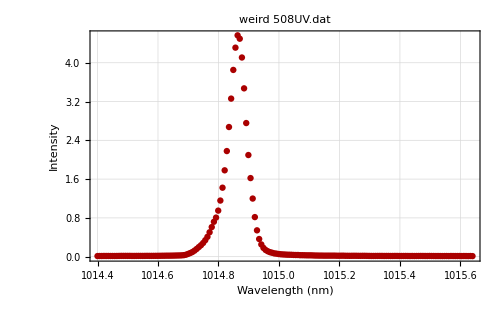

```mathematica
LinearDataPlot[FrameLabel->{"Wavelength (nm)","Intensity"}]
```